{0,1,-1,1,0}

{0,1/4,1/2,3/4,1}

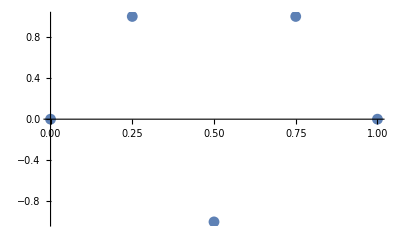

```mathematica
y={0,1,-1,1,0}
x={0,1/4,1/2,3/4,1}
ListPlot[Transpose[{x,y}]]
```

```mathematica
SqExp[ℓ_][a_,b_]:=Exp[-EuclideanDistance[a,b]^2/(2 ℓ^2)]
OrnsteinUhlenbeck[ℓ_][a_,b_]:=Exp[-EuclideanDistance[a,b]/ℓ]
Matern[ν_][ℓ_][a_,b_]:=With[{r=EuclideanDistance[a,b]},
2^(1-ν)/Gamma[ν]((√(2ν)r)/ℓ)^ν BesselK[ν,(√(2ν)r)/ℓ]]
```

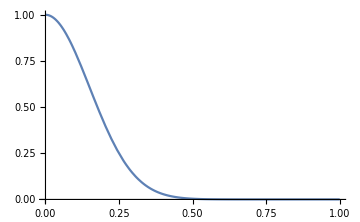
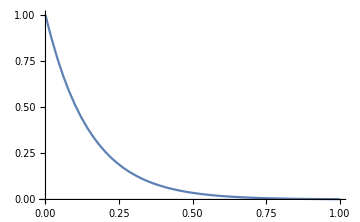

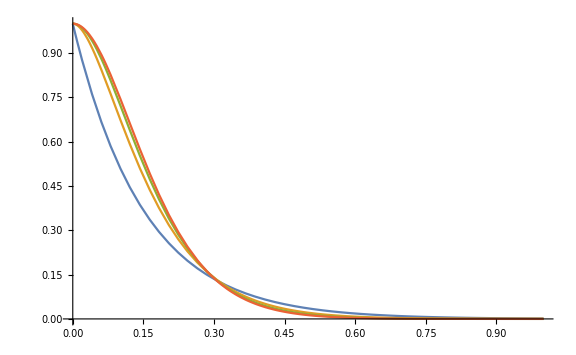

```mathematica
Row[{Plot[SqExp[0.15][0,x], {x,0,1},PlotRange->{0,1},ImageSize->Medium],
Plot[OrnsteinUhlenbeck[0.15][0,x], {x,0,1},PlotRange->{0,1},ImageSize->Medium]}]
Block[{x},
Plot[Evaluate[Table[Matern[ν][0.15][0,x],{ν,{1/2,3/2,5/2,7/2}}]],
 {x,0,1},PlotRange->{0,1},ImageSize->Large]]
```

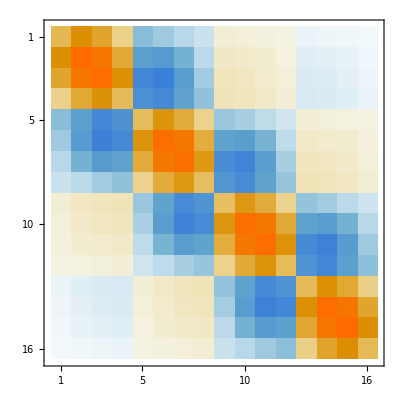

6.2939×10^6

```mathematica
l=0.1;
K=SqExp;
cov=Outer[K[l],x,x];
invcov= LinearSolve[cov,Method->"Cholesky"];
z=Select[Range[0,1,1/20],Function[{p},Abs[p-First[Nearest[x,p]]]>0.02]];
datacov=Outer[K[l],z,x];
μ=Dot[datacov,invcov[y]];
ccov=Outer[K[l],z,z]-Dot[datacov, invcov[Transpose[datacov]]];
MatrixPlot[ccov]
With[{s=SingularValueList[ccov]},First[s]/Last[s]]
```

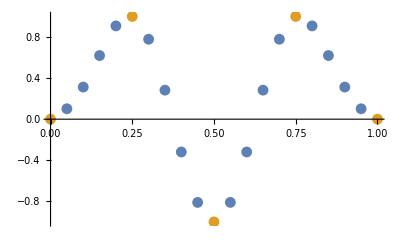

```mathematica
ListPlot[{Transpose[{z,μ}],Transpose[{x,y}]}]
```

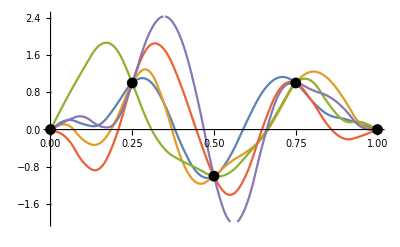

```mathematica
RandomVariate[MultinormalDistribution[μ,ccov],5];
Show[ListLinePlot[Map[Transpose[{z,#}]∪ Transpose[{x,y}]&,%],InterpolationOrder->2],ListPlot[Transpose[{x,y}],PlotStyle->Black]]
```

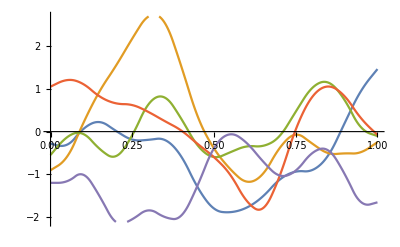

```mathematica
r=Range[0,1,1/20];
RandomVariate[MultinormalDistribution[ConstantArray[0,Length[r]],Outer[K[l],r,r]],5];
ListLinePlot[Map[Transpose[{r,#}]&,%],InterpolationOrder->2]
```

```mathematica
Manipulate[Plot[Matern[ν][ℓ][{0},{x}],{x,-1,1}],{{ν,0.575},0,2},{{ℓ,5/2},0,3}]
```

```mathematica
Clear[r]
Matern[3/2][ℓ][a_,b_]/.EuclideanDistance[a_,b_]->r//FullSimplify
Matern[5/2][ℓ][a_,b_]/.EuclideanDistance[a_,b_]->r//FullSimplify
```

(ⅇ^(-(√3 r)/ℓ) (√3 r+ℓ))/ℓ

(ⅇ^(-(√5 r)/ℓ) (5 r^2+3 √5 r ℓ+3 ℓ^2))/(3 ℓ^2)

```mathematica
l=0.15;
Clear[K]
Block[{ℓ,a,b,eqn},
eqn=FullSimplify[Matern[3/2][ℓ][a,b]];
K[ℓ_][a_,b_]:=Evaluate[eqn]];
Definition[K]
```

K[ℓ_][a_,b_]:=(ⅇ^(-(√3 EuclideanDistance[a,b])/ℓ) (ℓ+√3 EuclideanDistance[a,b]))/ℓ

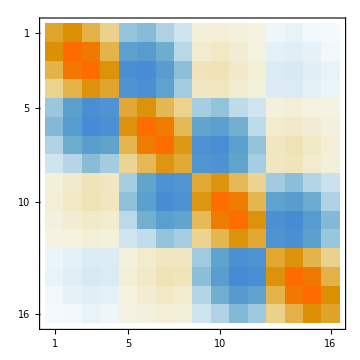
-Graphics-(1.35061
1.11151
0.862763
0.687592
0.200641
0.171632
0.139523
0.115722
0.0516596
0.0467038
0.0405171
0.0357256
0.021078
0.0202474
0.0191186
0.0182891)73.8478

```mathematica
cov=Outer[K[l],x,x];
invcov= LinearSolve[cov,Method->"Cholesky"];
z=Select[Range[0,1,1/20],Function[{p},Abs[p-First[Nearest[x,p]]]>0.02]];
datacov=Outer[K[l],z,x];
μ=Dot[datacov,invcov[y]];
ccov=Outer[K[l],z,z]-Dot[datacov, invcov[Transpose[datacov]]];
With[{s=SingularValueList[ccov]},
Row[{
MatrixPlot[ccov,ImageSize->Medium],
s//MatrixForm,
First[s]/Last[s]}]]
```

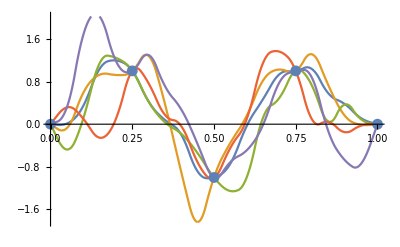

```mathematica
RandomVariate[MultinormalDistribution[μ,ccov],5];
Show[ListLinePlot[Map[Transpose[{z,#}]∪ Transpose[{x,y}]&,%],InterpolationOrder->2],ListPlot[Transpose[{x,y}]]]
```

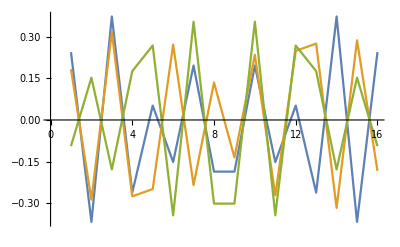

```mathematica
ListLinePlot[Eigenvectors[ccov]⟦-3;;-1⟧]
```